# The genetic code is not random

Current genetic table is optimized to support mutational changes and minimize the functional effect.

Said Munoz-Montero, Jun. 29,  2018

DNA encodes the proteins that perform a vast array of functions within organisms. The genetic code is a set of rules defining how the four-letter code of DNA is translated into the 20-letter code of amino acids, which are the building blocks of proteins. The genetic code is a set of three-letter combinations of nucleotides called codons, each of which corresponds to a specific amino acid or stop signal.

There are 64 possible permutations, or combinations, of three-letter nucleotide sequences that can be made from the four nucleotides. Of these 64 codons, 61 represent amino acids, and three are stop signals. Although each codon is specific for only one amino acid (or one stop signal), the genetic code is described as degenerate, or redundant, because a single amino acid may be coded for by more than one codon. It is also important to note that the genetic code does not overlap, meaning that each nucleotide is part of only one codon-a single nucleotide cannot be part of two adjacent codons. Furthermore, the genetic code is nearly universal, with only rare variations reported. But this configuration of the genetic table is not random.

## DNA

DNA, or deoxyribonucleic acid, is the hereditary material in humans and almost all other organisms. Nearly every cell in a person’s body has the same DNA.  DNA is composed by 4 nucleotides:

```mathematica
dnaBases=EntityClass["Chemical","DNABases"];
EntityValue[dnaBases,"BlackStructureDiagram","EntityAssociation"]
```

<|adenine→-Graphics-,guanine→-Graphics-,thymine→-Graphics-,cytosine→-Graphics-|>

In the coding protein of the DNA molecules, genetic information is encoded in three bases called triplets or codons. Every codon encodes the information for one amino acid and every amino acid can be encoded by one or more codons. For example, there are 6 different codons that encodes a Leucine:

```mathematica
DNA="TTATTGCTTCTCCTACTGTTTTTC" ;
WolframAlpha[DNA,{{"AminoAcidSequence",1},"FormattedData"}]
```

5'-3'  frame 1 | UUA | UUG | CUU | CUC | CUA | CUG | UUU | UUC
↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
Leu | Leu | Leu | Leu | Leu | Leu | Phe | Phe

The DNA structure is a double helix.

```mathematica
Options[makeDNA]={Background->White,ColorFunction->"Residue","HelixType"->"A",ImageSize->Automatic,"Hydrogens"->False,"Rendering"->"Structure","SingleStranded"->False,ViewPoint->Automatic};

makeDNA[seq_String,nucleotide_String,opts:OptionsPattern[]]:=Module[{params},params={"distro"->"make-na","seq_name"->"0","helix_type"->OptionValue["HelixType"],"f_acid_type"->nucleotide,"r_acid_type"->nucleotide,"description"->seq,"file_type"->"pdb","f_cid"->"A","r_cid"->"B","f_first_num"->1,"r_first_num"->1,"sugar_indi"->"asterisk","hydrogens"->If[TrueQ[OptionValue["Hydrogens"]],"yes","no"],"f_codelen"->1,"r_codelen"->1};
If[TrueQ[OptionValue["SingleStranded"]],AppendTo[params,"single_strand"->"SS"]];
ImportString[URLExecute["http://structure.usc.edu/cgi-bin/make-na/make-na.cgi",params,"String",Method->"POST"],"PDB",FilterRules[Join[{opts},Options[MakeDNA]],{Background,ColorFunction,ImageSize,"Rendering",ViewPoint}]]]

makeDNA[DNA,"dna"]
```

-Graphics3D-

There are some differences with RNA structure, one of nucleotides (Timine) is changed by an Uracile. The secondary structure becomes a single strand sequence.

```mathematica
RNA=StringReplace[DNA,"T"->"U"]
makeDNA[RNA,nucleotide="rna","HelixType"->"B","SingleStranded"->True,"Rendering"->"Wireframe"]
```

UUAUUGCUUCUCCUACUGUUUUUC

-Graphics3D-

As the central dogma of molecular biology states, our DNA undergoes processes that make DNA into an RNA sequence (transcription), and the latter to an amino acid sequence (translation); amino acids then fold into proteins.

In general terms, amino acids can be classified by chemical and physical properties that makes the amino acids fold in different ways and allow the diversity in structures.

-Graphics-

20 different amino acids are generally used for living organisms.

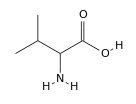
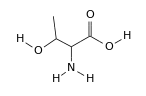
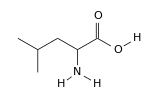
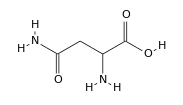
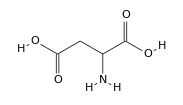
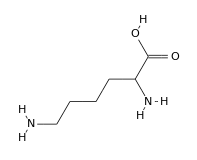
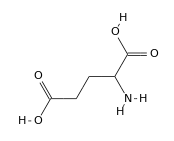
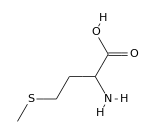
<|glycine→-Graphics-,L-alanine→-Graphics-,L-serine→-Graphics-,L-proline→-Graphics-,L-valine→-Graphics-,L-threonine→-Graphics-,L-cysteine→-Graphics-,L-leucine→-Graphics-,L-asparagine→-Graphics-,L-aspartic acid→-Graphics-,L-glutamine→-Graphics-,L-lysine→-Graphics-,L-glutamic acid→-Graphics-,L-methionine→-Graphics-,DL-histidine→-Graphics-,L-phenylalanine→-Graphics-,L-arginine→-Graphics-,L-tyrosine→-Graphics-,L-tryptophan→-Graphics-,L-isoleucine→-Graphics-|>

```mathematica
aminoAcids=EntityClass["Chemical","AminoAcids"];
EntityValue[#, "BlackStructureDiagram", "EntityAssociation"]& @ aminoAcids
```

That amino acids in the same biochemical pathway are coded by related codons does not necessarily explain the observation that amino acids that have similar physicochemical properties also have similar codons.

Amino acids fold into 3D functional structures. For example, the following protein is an oncogene repressor encoded by the gene MIA (Melanoma Inhibitory Activity)

```mathematica
ProteinData["MIA","Sequence"]
ProteinData["MIA","MoleculePlot"]
```

MARSLVCLGVIILLSAFSGPGVRGGPMPKLADRKLCADQECSHPISMAVALQDYMAPDCRFLTIHRGQVVYVFSKLKGRGRLFWGGSVQGDYYGDLAARLGYFPSSIVREDQTLKPGKVDVKTDKWDFYCQ

-Graphics3D-

The genetic code is the biochemical system that establishes the rules by which the nucleotide sequence of a gene is transcribed into the mRNA codon sequence and next the mRNA is translated into the amino acid sequence of the corresponding protein.

```mathematica
aminoAcid2Codon=AssociationThread[ChemicalData["AminoAcids"]-> ChemicalData["AminoAcids","Codons"]]
```

<|glycine→{GGU,GGC,GGA,GGG},L-alanine→{GCU,GCC,GCA,GCG},L-serine→{UCU,UCC,UCA,UCG,AGU,AGC},L-proline→{CCU,CCC,CCA,CCG},L-valine→{GUU,GUC,GUA,GUG},L-threonine→{ACU,ACC,ACA,ACG},L-cysteine→{UGU,UGC},L-isoleucine→{AUU,AUC,AUA},L-leucine→{UUA,UUG,CUU,CUC,CUA,CUG},L-asparagine→{AAU,AAC},L-aspartic acid→{GAU,GAC},L-glutamine→{CAA,CAG},L-lysine→{AAA,AAG},L-glutamic acid→{GAA,GAG},L-methionine→{AUG},L-histidine→{CAU,CAC},L-phenylalanine→{UUU,UUC},L-arginine→{CGU,CGC,CGA,CGG,AGA,AGG},L-tyrosine→{UAU,UAC},L-tryptophan→{UGG}|>

```mathematica
aaCodon={{"A",{"GCT","GCC","GCA","GCG"}},{"R",{"CGT","CGC","CGA","CGG","AGA","AGG"}},{"N",{"AAT","AAC"}},{"D",{"GAT","GAC"}},{"C",{"TGT","TGC"}},{"Q",{"CAA","CAG"}},{"E",{"GAA","GAG"}},{"G",{"GGT","GGC","GGA","GGG"}},{"H",{"CAT","CAC"}},{"I",{"ATT","ATC","ATA"}},{"L",{"TTA","TTG","CTT","CTC","CTA","CTG"}},{"K",{"AAA","AAG"}},{"M",{"ATG"}},{"F",{"TTT","TTC"}},{"P",{"CCT","CCC","CCA","CCG"}},{"S",{"TCT","TCC","TCA","TCG","AGT","AGC"}},{"T",{"ACT","ACC","ACA","ACG"}},{"W",{"TGG"}},{"Y",{"TAT","TAC"}},{"V",{"GTT","GTC","GTA","GTG"}},{"*",{"TAA","TGA","TAG"}}};
dnaToProteinTable=<|Flatten[Table[Rule@@@Partition[Riffle[aaCodon[[i,2]],aaCodon[[i,1]],{2,-1,2}],2],{i,21}]]|>
```

<|GCT→A,GCC→A,GCA→A,GCG→A,CGT→R,CGC→R,CGA→R,CGG→R,AGA→R,AGG→R,AAT→N,AAC→N,GAT→D,GAC→D,TGT→C,TGC→C,CAA→Q,CAG→Q,GAA→E,GAG→E,GGT→G,GGC→G,GGA→G,GGG→G,CAT→H,CAC→H,ATT→I,ATC→I,ATA→I,TTA→L,TTG→L,CTT→L,CTC→L,CTA→L,CTG→L,AAA→K,AAG→K,ATG→M,TTT→F,TTC→F,CCT→P,CCC→P,CCA→P,CCG→P,TCT→S,TCC→S,TCA→S,TCG→S,AGT→S,AGC→S,ACT→T,ACC→T,ACA→T,ACG→T,TGG→W,TAT→Y,TAC→Y,GTT→V,GTC→V,GTA→V,GTG→V,TAA→*,TGA→*,TAG→*|>

Grantham score

The Grantham score attempts to predict the distance between two amino acids, in an evolutionary sense. A lower Grantham score reflects less evolutionary distance. A higher Grantham score reflects a greater evolutionary distance. Higher Grantham scores are considered more deleterious.The distance scores published by Grantham range from 5 to 215.

A substitution of isoleucine for leucine, or of leucine for isoleucine, has a score of 5 (and is predicted to be tolerated). A substitution cysteine for tryptophan, or of tryptophan for cysteine, has a score of 215. Any variation involving cysteine has a high or very high Grantham score (and is predicted to be deleterious).

The Grantham score attempts to predict the distance between two amino acids, in an evolutionary sense. A lower Grantham score reflects less evolutionary distance. A higher Grantham score reflects a greater evolutionary distance. Higher Grantham scores are considered more deleterious.The distance scores published by Grantham range from 5 to 215.

A substitution of isoleucine for leucine, or of leucine for isoleucine, has a score of 5 (and is predicted to be tolerated). A substitution cysteine for tryptophan, or of tryptophan for cysteine, has a score of 215. Any variation involving cysteine has a high or very high Grantham score (and is predicted to be deleterious).

```mathematica
grantham=SemanticImport["https://gist.githubusercontent.com/said3427/dcafd8973fa8bdb9319c7cfe166e6815/raw/6af674602c87dc27bb59c1497d837967738357ca/grantham_matrix.tsv"]
row={"A","R","N","D","C","Q","E","G","H","I","L","K","M","F","P","S","T","W","Y","V"};
pos=AssociationThread[row,Range[20]]
```

Dataset[<>]

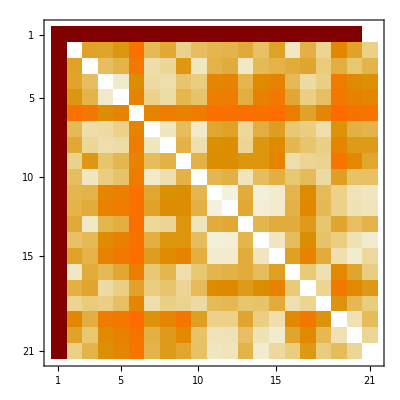

```mathematica
MatrixPlot[grantham]
```

If we can simulate different mutations in DNA, we could have an idea about the DNA stability to mutations.

```mathematica
randomGeneticTable=AssociationThread[Keys[dnaToProteinTable], RandomSample[Values[dnaToProteinTable]]]
```

<|GCT→G,GCC→K,GCA→I,GCG→S,CGT→N,CGC→E,CGA→R,CGG→R,AGA→L,AGG→P,AAT→R,AAC→A,GAT→G,GAC→I,TGT→R,TGC→K,CAA→T,CAG→S,GAA→S,GAG→V,GGT→G,GGC→T,GGA→Q,GGG→N,CAT→P,CAC→*,ATT→G,ATC→L,ATA→L,TTA→R,TTG→P,CTT→*,CTC→Y,CTA→D,CTG→A,AAA→H,AAG→C,ATG→M,TTT→A,TTC→S,CCT→L,CCC→E,CCA→D,CCG→L,TCT→C,TCC→T,TCA→F,TCG→T,AGT→I,AGC→S,ACT→S,ACC→V,ACA→R,ACG→H,TGG→W,TAT→L,TAC→P,GTT→Q,GTC→*,GTA→Y,GTG→V,TAA→F,TGA→V,TAG→A|>

```mathematica
GranthamDNA["A","T"]
```

58

```mathematica
sequence=GenomeData["SCNN1A","FullSequence"];
StringLength[sequence]
```

28703

```mathematica
MatrixPlot[grantham]
```

-Graphics-

#### Simulation of DNA mutations

```mathematica
dnaseq1="ATGGACAATGCGATAAGCACTCACGAAGGTGAGAATGAGACTATTTGCATGGCAACCGAACGAATAGCGCTGTAA";
proteinSeq="MDNAISTHEGENETICMATERIAL*";
```

```mathematica
Manipulate[
Module[
{mutpos,mutpointseq,mutfsPlusseq,mutfsMinusseq,mutseq,mutproteinseq},
mutpos={SeedRandom[seed];RandomSample[Range[1,69],1]}[[1]];
mutpointseq=StringJoin[Flatten[ReplacePart[Characters[dnaseq1],mutpos->RandomSample[Complement[{"A","C","G","T"},Take[Characters[dnaseq1],mutpos]],1]]]];
mutfsPlusseq=StringJoin[Flatten[Insert[Characters[dnaseq1],RandomSample[{"A","C","G","T"},1],mutpos]]];
mutfsMinusseq=StringJoin[Flatten[Flatten[ReplacePart[Characters[dnaseq1],mutpos->{}]]]];mutseq={mutpointseq,mutfsPlusseq,mutfsMinusseq}[[type]];mutproteinseq=If[(StringJoin/@Partition[Characters[mutseq],3]/.dnaToProteinTable)[[1]]≠"M",Table["",{25}],If[Union[StringFreeQ[StringJoin/@Partition[Characters[mutseq],3]/.dnaToProteinTable,"*"]][[1]],StringJoin/@Partition[Characters[mutseq],3]/.dnaToProteinTable,PadRight[Take[StringJoin/@Partition[Characters[mutseq],3]/.dnaToProteinTable,Position[StringJoin/@Partition[Characters[mutseq],3]/.dnaToProteinTable,"*"][[1,1]]],25,""]]];
Grid[{{Style[Grid[{StringJoin/@Partition[Characters[dnaseq1],3],
StringJoin/@Partition[Characters[dnaseq1],3]/.dnaToProteinTable,StringJoin/@Partition[PadRight[Characters[mutseq],75,"T"],3],
mutproteinseq},Frame->All,Background->{None,None,Join[(Flatten[{3,#}]->Hue[0,0.3,1]&)/@Position[Equal@@@Transpose[{StringJoin/@Partition[PadRight[Characters[dnaseq1],75,""],3],StringJoin/@Partition[PadRight[Characters[mutseq],75,"A"],3]}],False],
(Flatten[{4,#}]->Hue[0.55,0.3,1]&)/@Position[Equal@@@Transpose[{Characters[proteinSeq],PadRight[mutproteinseq,25,""]}],False]]},Alignment->Center,Spacings->{0.0,1.5},FrameStyle->GrayLevel[0.6]],FontFamily->"Courier",14,FontTracking->"SemiCondensed"]},
{Style[StringJoin[Insert[mutproteinseq[[2;;-2]]," ",{{4},{6},{9},{16}}]],FontFamily->"Courier",20]}},Spacings->{0,2}]],
{{seed,1,""},Button["mutate",seed={SeedRandom[];RandomInteger[1000]}[[1]]]&},{{type,1,"mutation "},{1->"1 bp substitution",2->"1 bp insertion",3->"1 bp deletion"}},SaveDefinitions->True]
```

## Further explorations

How a 4-nucleotides genetic table will affect the genetic variability of species?

## Author contact information

said3427@gmail.com